```mathematica
NIntegrate[Exp[-x]/(x^(-1/4)-2)^2,{x,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0644376}. NIntegrate obtained 2902.14 and 2427.65 for the integral and error estimates.

2902.14

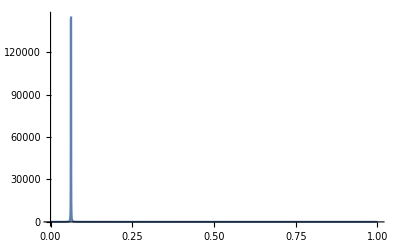

```mathematica
Plot[Exp[-x]/(x^(-1/4)-2)^2,{x,0,1},PlotRange->All]
```

```mathematica
γ=-1/4;
α = .5;
β = α^(1/γ);
ψ[x_]:=Exp[-x];
```

```mathematica
ϕ[x_]:=(ψ[x]/(x^γ-α)^2)*(x-β)^2;
ϕβ:=N@Limit[ϕ[x],x->β];
```

```mathematica
intagrale=NIntegrate[(ϕ[β+x]+ϕ[β-x]-2*ϕβ)/x^2,{x,0,β}]+NIntegrate[(ϕ[x]-2*ϕβ)/(x-β)^2,{x,2*β,Infinity}]
```

4.71953

```mathematica
ϵ=.1;
```

```mathematica
NIntegrate[ψ[x]/(x^γ-α)^2,{x,0,β-ϵ}]+NIntegrate[ψ[x]/(x^γ-α)^2,{x,β+ϵ,Infinity}]
```

4.75625

```mathematica
NIntegrate[ϕ[x],{x,0,.5*β}]+NIntegrate[ϕ[x],{x,4*β,Infinity}]
```

893.968

```mathematica
intagrale=NIntegrate[(ϕ[β+x]+ϕ[β-x]-2*ϕβ)/x^2,{x,0,.5*β}]+NIntegrate[(ϕ[x]-2*ϕβ)/(x-β)^2,{x,4*β,Infinity}]
```

```mathematica
integraletest[ϵ_]:=(NIntegrate[ψ[x]/(x^γ-α)^2,{x,0,β-ϵ}]+NIntegrate[ψ[x]/(x^γ-α)^2,{x,β+ϵ,Infinity}])/4.719531116001872;
```

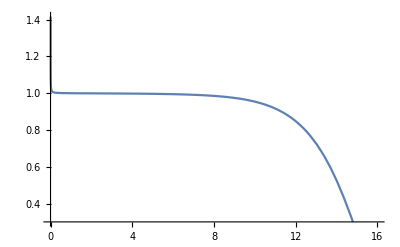

```mathematica
Plot[integraletest[ϵ],{ϵ,β/100000000,β}]
```

```mathematica
ϕβ/ψ[β]
```

16384.

```mathematica
1/(γ*((2*γ-1)*β^(2*(γ-1))-α*(γ-1)*β^(γ-2)))
```

16384.

```mathematica
Limit[((x-a^(1/g))/(x^g-a))^2,x->a^(1/g)]
```

0

```mathematica
Limit[((x-α^(1/γ))/(x^γ-α))^2,x->α^(1/γ)]
```

16384.